#### Kirill Zakharov Trigonometric interpolation

fun - исходная функция
n - натуральное число, степень тригонометрического полинома
L - период функции
point - переменная, от которой считается полученный полином
xm - интерполяционная сетка
ym - значения функции в узлах интерполяции

```mathematica
trigInter[fun_,n_,L_,point_]:=Module[{n2=2(n+1),xm,ym,a0,ak,bk},
xm=Table[-L/n2 m+L/(2n2),{m,1,n2}];
ym=fun/@xm//N;
a0 = 1/n2 Sum[ym⟦i⟧,{i,1,n2}];
ak=Table[2/n2 Sum[ym⟦i⟧Cos[k(2 Pi/n2 i+Pi/n2)],{i,1,n2}],{k,1,n}];
bk=Table[2/n2 Sum[ym⟦i⟧Sin[k(2 Pi/n2 i+Pi/n2)],{i,1,n2}],{k,1,n}];
a0+Sum[ak⟦k⟧Cos[k *2 Pi/L*point]+bk⟦k⟧Sin[k *2 Pi/L*point],{k,1,n}]]
```

#### Example

Точки в которых хотим произвести интерполяцию

```mathematica
interPoint={2Pi,3.5Pi,4.5Pi,3.3Pi,2.1Pi,0.2Pi,1.3Pi};
```

Тригонометрический полином

```mathematica
trigInter[Cos,10,2Pi,x]
```

2.52323×10^-17+0.959493 Cos[x]+2.01859×10^-17 Cos[2 x]+3.02788×10^-17 Cos[3 x]+1.00929×10^-17 Cos[5 x]+2.01859×10^-17 Cos[6 x]-5.04647×10^-18 Cos[8 x]-7.5697×10^-17 Cos[9 x]+0.281733 Sin[x]-5.04647×10^-18 Sin[2 x]+5.04647×10^-18 Sin[3 x]-8.07435×10^-17 Sin[5 x]-1.00929×10^-17 Sin[6 x]-4.03717×10^-17 Sin[7 x]+1.00929×10^-17 Sin[9 x]

Значения полученного тригонометрического полинома в точка интерполяции

```mathematica
trigInter[Cos,10,2Pi,#]&/@interPoint
```

{0.959493,-0.281733,0.281733,-0.791902,0.999592,0.941844,-0.791902}

#### Test

Зеленные точки - это значения, полученные при помощи построенного интерполянта, а красные - значения исходной функции.

```mathematica
new=trigInter[Cos,10,2Pi,#]&/@interPoint;
initialData=Cos/@interPoint;
lst1={interPoint,new}//Transpose;
lst2={interPoint,initialData}//Transpose;
```

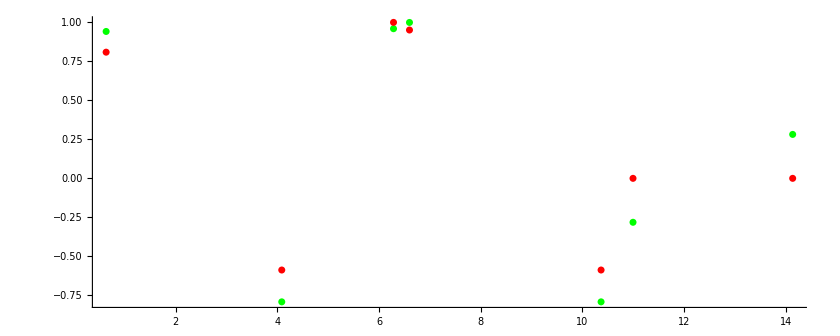

```mathematica
Show[Graphics[{Green,PointSize[0.006],Point/@lst1,Red,PointSize[0.006],Point/@lst2},Axes->True]]
```

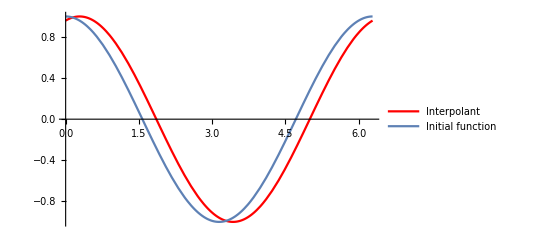

```mathematica
Show[Plot[trigInter[Cos,10,2Pi,k],{k,0,2Pi},PlotStyle->Red,PlotLegends->{"Interpolant"}],Plot[Cos[k],{k,0,2Pi},PlotLegends->{"Initial function"}]]
```